# Spacelike collinear 5-point examples

Seed diagnostic at In[1]-In[5]. Current preselected HRF results at In[6]-In[12]. Regenerate scans at In[13]-In[14]. Polynomial study at In[23].

Kernel "Local" (Evaluation > Notebook's Kernel). On open, init prints a reminder only. Restart Kernel once manually, then run In[1] onward. Do not put RestartKernel in auto-run init cells.

```mathematica
Print["HRF notebook loaded. Before In[1], use Evaluation > Restart Kernel once (manual)."];
```

Run the seed diagram diagnostic (In[1]-In[5]) first. The full 7/8-propagator topology scan is disabled until the seed case finds a hidden region with a single generator.

## Seed diagram diagnostic (run first)

Fast seed-only workflow (matches working binomial Ex03): polynomial f_k kin-normalized and Mandelstam-linear, SingleProduct generator g = product of all simultaneously admissible f_k. In[4] should show SafeSingleProductSetCount >= 1 before In[5].

```mathematica
$HRFEx03RunFullTopologyScanQ=False;$HRFEx03UsePolynomialFactorsQ=True;$HRFEx03ObstructionProgressQ=True;$HRFExampleVerbose=False;$HRFVerboseScaling=False;$HRFScalingReport=False;$HRFQuietReports=False;$HRFFindObstructionsStopOnFirstAdmissibleQ=False;$HRFCandidateGeneratorSetLimit=64;$HRFPolynomialMaxMonomials=12;$HRFPolynomialRequireKinematicDomainQ=False;$HRFUseGeneratorPhysicsFilterQ=True;Get[FileNameJoin[{NotebookDirectory[],"HiddenRegionFinder.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"HRF_Example03CollinearCore.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"HRF_PolynomialCancellationFactors.wl"}]];hrfInstallPolynomialCancellationPatch[];Get[FileNameJoin[{NotebookDirectory[],"HRF_Example03SeedStudy.wl"}]];hrfEx03SeedStudyLoad[];
```

[loaded] generator physics filter (kin pairing + sector quotient).

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[patch loaded] Obstruction reporting: F_0^restricted - Obstruction = F_SL; Obstruction + F_SL = F_0^restricted.

[loaded] Example 01 common reporting helpers.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[loaded] polynomial-factor reporting helpers.

[loaded] HRF_WideAngleBoundaryDiagnostic.wl — try hrfWideAngleBoundaryDiagnostic["HyperCrownX11"]

[Example 03 core] seed vars=6  ThreeLoopVertex vars=9  (no graph/boundary scans).

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[Example 03 seed] loaded. Evaluate hrfEx03SeedRouteComparison[], hrfEx03SeedFivePointRouteStudy[], hrfEx03RunSeedObstruction[].

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[loaded] five-point reporting helpers.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

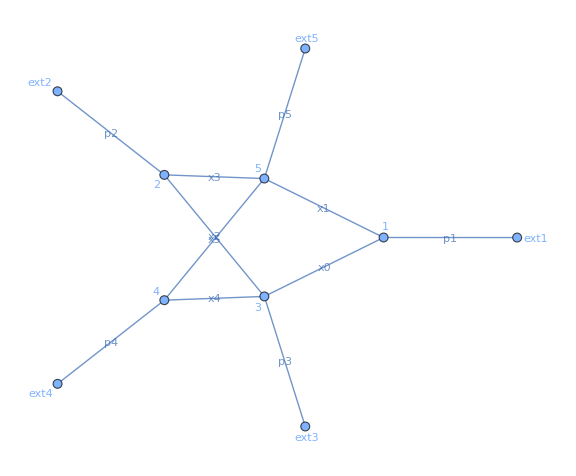

```mathematica
drawGraphFromPySecDecInput[seedInternalLines,seedExternalLines]
```

```mathematica
hrfEx03SeedFactorTable[]
```

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

```mathematica
hrfEx03SeedGeneratorAudit[]
```

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

<|GeneratorMode→SingleProduct,UseExtendedFactors→False,RelaxSingleProductDegreeQ→False,SkipPDFFindInstanceQ→False,SafeFactorCount→2,GeneratorEligibleFactorCount→2,BinomialEligibleFactorCount→2,SingleProductGeneratorFactorCount→2,SimultaneouslyAdmissibleLegacyBinomialPoolQ→True,SafeSingleProductSets→{{-x1 x2 x4-x1 x3 x4-x x0 x2 x5-x x0 x3 x5+x1 x2 x4 z+x x0 x2 x5 z}},SafeSingleProductSetCount→1,SimultaneouslyAdmissibleGeneratorPoolQ→True,FullProductDegreeAdmissibleQ→True,NonlinearSafeFactors→{}|>

Route comparison: canonical f_k (one row per class), all eligible pair products with rejection reasons, obstruction trial stages. Seed5pt only — ThreeLoopVertex is at In[5c] and In[14].

```mathematica
Ex03RouteComparison=hrfEx03SeedRouteComparison[];Ex03RouteComparison["Summary"]
```

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[Example 03] finding cancellation factors (6 vars, maxSize Automatic)...

[Example 03] 2 cancellation factors; building generator trials (mode SingleProduct)...

[Example 03] obstruction search: 2 generator trials (cap 64); max obstruction size computed per set from |F| - sum|monomials(g_i)|

[Example 03] trial 1/2 (|gens|=1, kin-free=0)

13:40:50  [coverage routine] findCoverageLPScaling FAST entered vars=6 maxAbs=5 bruteBox=46655

13:40:50  [coverage candidate generation] method=nullspace vars=6 maxAbs=5 monomialRows=4 homogeneityRank=2 nullspaceDim=4 coeffBox=14640

13:40:50  [coverage candidates] method=FSLNullspaceCoefficients candidateCount=797 exhaustiveQ=True

13:40:50  [coverage candidate testing start] candidates=797

13:40:50  [coverage candidate testing end] accepted=99

13:40:50  [coverage routine] findCoverageLPScaling FAST entered vars=6 maxAbs=5 bruteBox=46655

13:40:50  [coverage candidate generation] method=nullspace vars=6 maxAbs=5 monomialRows=6 homogeneityRank=3 nullspaceDim=3 coeffBox=1330

13:40:50  [coverage candidates] method=FSLNullspaceCoefficients candidateCount=175 exhaustiveQ=True

13:40:50  [coverage candidate testing start] candidates=175

13:40:50  [coverage candidate testing end] accepted=0

13:40:50  [coverage coordinate-uniform scan start] box=46655 maxAbs=5

13:40:50  [coverage coordinate-uniform scan end] uniformCandidates=215 accepted=0

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

<|RootCauseSummary→{Both routes select the same 2 canonical f_k after cleanup; polynomial pool is a superset for this seed.,Raw (1-z)-shelled and core f_k are one canonical class after Factor stripping of non-x_i shells.},Counts→<|LegacyBinomialSafe→2,PolynomialSafeCanonical→2,BinomialRouteSelected→2,PolynomialRouteSelected→2,PolynomialAdmissiblePairs→1|>,HiddenRegionQ→<|PolynomialObstructionScan→True|>,ColumnGuide→{CanonicalFactorTable / FactorTable: one row per canonical f_k (all safe-pool classes).,ChosenForGeneratorQ: picked by SingleProduct resolver on polynomial pool (not all admissible pairs).,GeneratorPairAuditTable: kin-prefiltered pairs g=f1*f2 (no kin-square / shared kin var); Factor1 has lower x-degree.,ObstructionTrialTable: after generator fixed, SL decomposition, sector PDF, scaling / HiddenRegionQ.,Selected in route comparison = resolver choice for that safe pool, not the only admissible generator.}|>

```mathematica
Ex03RouteComparison["CanonicalFactorTable"]
```

```mathematica
Ex03RouteComparison["GeneratorPairAuditTable"]
```

```mathematica
Ex03RouteComparison["GeneratorSelectionTable"]
```

Optional: every raw harvest variant.

```mathematica
Ex03RouteComparison["FactorTableVerbose"]
```

```mathematica
Ex03SeedObstruction=hrfEx03RunSeedObstruction[];KeyTake[Ex03SeedObstruction,{"HiddenRegionQ","Generators","AttemptSummary"}]
```

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[Example 03] finding cancellation factors (6 vars, maxSize Automatic)...

[Example 03] 2 cancellation factors; building generator trials (mode SingleProduct)...

[Example 03] obstruction search: 1 generator trials (cap 64); max obstruction size computed per set from |F| - sum|monomials(g_i)|

[Example 03] trial 1/1 (|gens|=1, kin-free=0)

13:40:51  [coverage routine] findCoverageLPScaling FAST entered vars=6 maxAbs=5 bruteBox=46655

13:40:51  [coverage candidate generation] method=nullspace vars=6 maxAbs=5 monomialRows=4 homogeneityRank=2 nullspaceDim=4 coeffBox=14640

13:40:52  [coverage candidates] method=FSLNullspaceCoefficients candidateCount=797 exhaustiveQ=True

13:40:52  [coverage candidate testing start] candidates=797

13:40:52  [coverage candidate testing end] accepted=99

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[Example 03 seed] seed obstruction: Safe=2 eligible=2 simultaneous=True SingleProductSets=1 HiddenRegionQ=True (ThreeLoopVertex: evaluate In[5c] or In[14a]-[14b])

<|HiddenRegionQ→True,Generators→{(x1 x4+x x0 x5) (-x2-x3+x2 z)},AttemptSummary→<|TrialCount→1,CandidateGeneratorCount→1,PerGeneratorAdmissibleCount→1,CandidateUnionPDFAdmissibleCount→1,ObstructionFindInstanceCount→1,AdmissibleSLSectorCount→1,ValidObstructionCount→1,HiddenRegionWithValidScalingCount→1,ScalingEvaluatedOnValidTrialsQ→True,GeneratorCountHistogram→<|1→1|>,StopOnFirstValidObstructionQ→False,StoppedEarlyOnValidObstructionQ→False|>|>

```mathematica
Ex03SeedObstruction["GeneratorPairAuditTable"]
```

```mathematica
Ex03SeedObstruction["ObstructionTrialTable"]
```

## Seed5pt vs ThreeLoopVertex (generator audit)

Both topologies: canonical f_k table (Topology column), pair audit, binomial vs polynomial resolver. Vertex obstruction skipped by default.

```mathematica
Ex03FivePointRoutes=hrfEx03SeedFivePointRouteStudy[];Ex03FivePointRoutes["GeneratorSelectionTable"];Ex03FivePointRoutes["CanonicalFactorTable"];Ex03FivePointRoutes["GeneratorPairAuditTable"]
```

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[Example 03] finding cancellation factors (6 vars, maxSize Automatic)...

[Example 03] 2 cancellation factors; building generator trials (mode SingleProduct)...

[Example 03] obstruction search: 1 generator trials (cap 64); max obstruction size computed per set from |F| - sum|monomials(g_i)|

[Example 03] trial 1/1 (|gens|=1, kin-free=0)

13:41:05  [coverage routine] findCoverageLPScaling FAST entered vars=6 maxAbs=5 bruteBox=46655

13:41:05  [coverage candidate generation] method=nullspace vars=6 maxAbs=5 monomialRows=4 homogeneityRank=2 nullspaceDim=4 coeffBox=14640

13:41:05  [coverage candidates] method=FSLNullspaceCoefficients candidateCount=797 exhaustiveQ=True

13:41:05  [coverage candidate testing start] candidates=797

13:41:05  [coverage candidate testing end] accepted=99

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 12 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

```mathematica
Ex03FivePointRoutes["ThreeLoopVertex"]["NonBinomialGeneratorSelectedQ"];Ex03FivePointRoutes["HiddenRegionQ"]
```

<|Seed5pt→True,ThreeLoopVertex→Missing[Skipped]|>

## Current preselected 5-point scan results

Collaborator-facing summary of the current polynomial HRF scan. These cells read the saved outputs from HRF_RunPreselected5ptScan.wl; they do not run HRF. Boundary ZeroVars are diagnostic strata where HRF found a hidden region. The graph catalogue deliberately draws the original topologies, because those are the objects passed onward to HRF.

```mathematica
$HRFQuietReports=True;Get[FileNameJoin[{NotebookDirectory[],"HRF_Example03PreselectedResults.wl"}]];
```

```mathematica
hrfEx03PreselectedRunInstructions[]
```

Reproducibility notes
The tables below read saved scan outputs.  To regenerate them, run the two command cells in this section from a fresh kernel.
Observed wall time on this machine: the 70-topology interior scan took a few minutes; the codimension-1/2 boundary scan took about 8 minutes.  Times vary with WolframKernel load.
Boundary ZeroVars identify the diagnostic stratum where HRF found a hidden region.  The drawn graph remains the original topology and is the object passed onward to HRF.

```mathematica
hrfEx03PreselectedScanSummary[]
```

All topologies with at least one accepted interior or boundary HR stratum. The internal labels x0,x1,... are the Feynman parameters in the scaling vectors; external leg p_i emerges from vertex i.

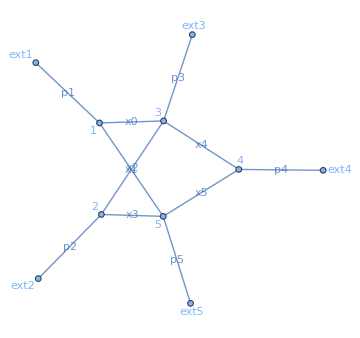
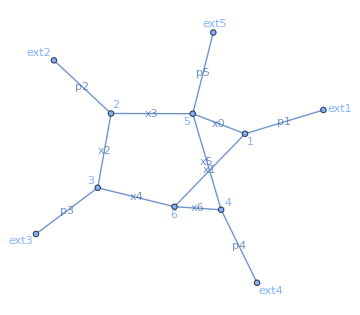
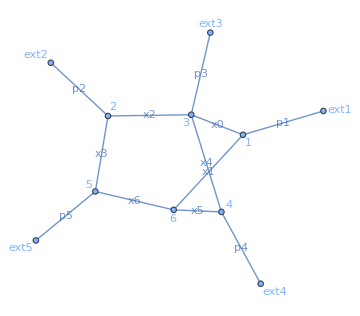
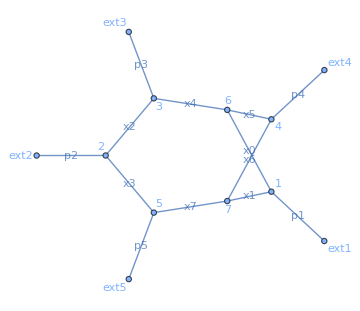
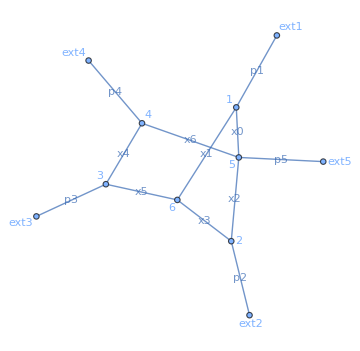
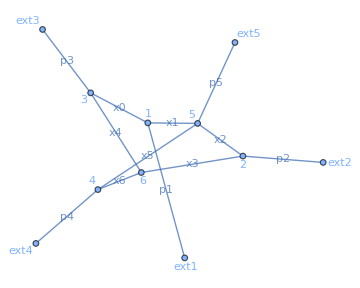
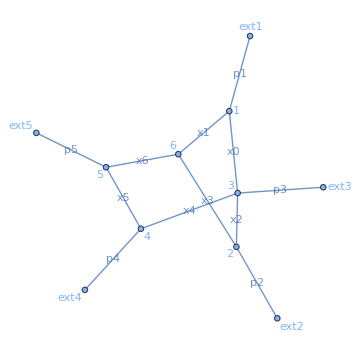
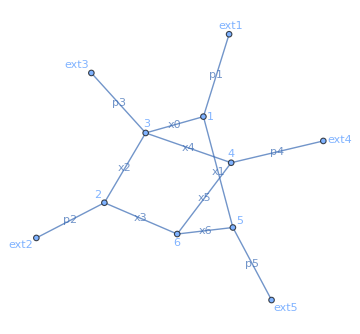
Graph | Propagators | Family:index | Drawing | Internal variables | External legs
G_bulletbullet | 6 | nonplanar:5 | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 5}
x2 = edge {2, 3}
x3 = edge {2, 5}
x4 = edge {4, 3}
x5 = edge {4, 5} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_tbullet | 7 | nonplanar:50 | -Graphics- | x0 = edge {1, 5}
x1 = edge {1, 6}
x2 = edge {2, 3}
x3 = edge {2, 5}
x4 = edge {3, 6}
x5 = edge {4, 5}
x6 = edge {4, 6} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_bullett | 7 | nonplanar:31 | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 6}
x2 = edge {2, 3}
x3 = edge {2, 5}
x4 = edge {4, 3}
x5 = edge {4, 6}
x6 = edge {5, 6} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_tt | 8 | nonplanar:90 | -Graphics- | x0 = edge {1, 6}
x1 = edge {1, 7}
x2 = edge {2, 3}
x3 = edge {2, 5}
x4 = edge {3, 6}
x5 = edge {4, 6}
x6 = edge {4, 7}
x7 = edge {5, 7} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_sbullet | 7 | nonplanar:57 | -Graphics- | x0 = edge {1, 5}
x1 = edge {1, 6}
x2 = edge {2, 5}
x3 = edge {2, 6}
x4 = edge {3, 4}
x5 = edge {3, 6}
x6 = edge {4, 5} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_ubullet | 7 | nonplanar:29 | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 5}
x2 = edge {2, 5}
x3 = edge {2, 6}
x4 = edge {3, 6}
x5 = edge {4, 5}
x6 = edge {4, 6} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_bullets | 7 | nonplanar:32 | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 6}
x2 = edge {2, 3}
x3 = edge {2, 6}
x4 = edge {4, 3}
x5 = edge {4, 5}
x6 = edge {5, 6} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_bulletu | 7 | nonplanar:28 | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 5}
x2 = edge {2, 3}
x3 = edge {2, 6}
x4 = edge {4, 3}
x5 = edge {4, 6}
x6 = edge {5, 6} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_ss | 8 | nonplanar:99 | -Graphics- | x0 = edge {1, 6}
x1 = edge {1, 7}
x2 = edge {2, 6}
x3 = edge {2, 7}
x4 = edge {3, 4}
x5 = edge {3, 6}
x6 = edge {4, 5}
x7 = edge {5, 7} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_su | 8 | nonplanar:136 | -Graphics- | x0 = edge {1, 5}
x1 = edge {1, 6}
x2 = edge {2, 6}
x3 = edge {2, 7}
x4 = edge {3, 4}
x5 = edge {3, 6}
x6 = edge {4, 7}
x7 = edge {5, 7} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_us | 8 | nonplanar:116 | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 6}
x2 = edge {2, 6}
x3 = edge {2, 7}
x4 = edge {3, 7}
x5 = edge {4, 5}
x6 = edge {4, 7}
x7 = edge {5, 6} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_uu | 8 | nonplanar:78 | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 5}
x2 = edge {2, 6}
x3 = edge {2, 7}
x4 = edge {3, 6}
x5 = edge {4, 6}
x6 = edge {4, 7}
x7 = edge {5, 7} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_ts | 8 | nonplanar:144 | -Graphics- | x0 = edge {1, 6}
x1 = edge {1, 7}
x2 = edge {2, 3}
x3 = edge {2, 6}
x4 = edge {3, 7}
x5 = edge {4, 5}
x6 = edge {4, 7}
x7 = edge {5, 6} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_st | 8 | nonplanar:151 | -Graphics- | x0 = edge {1, 6}
x1 = edge {1, 7}
x2 = edge {2, 5}
x3 = edge {2, 6}
x4 = edge {3, 4}
x5 = edge {3, 6}
x6 = edge {4, 7}
x7 = edge {5, 7} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_ut | 8 | nonplanar:114 | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 6}
x2 = edge {2, 5}
x3 = edge {2, 7}
x4 = edge {3, 7}
x5 = edge {4, 6}
x6 = edge {4, 7}
x7 = edge {5, 6} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5
G_tu | 8 | nonplanar:133 | -Graphics- | x0 = edge {1, 5}
x1 = edge {1, 6}
x2 = edge {2, 3}
x3 = edge {2, 7}
x4 = edge {3, 6}
x5 = edge {4, 6}
x6 = edge {4, 7}
x7 = edge {5, 7} | p1 emerges from vertex 1
p2 emerges from vertex 2
p3 emerges from vertex 3
p4 emerges from vertex 4
p5 emerges from vertex 5

```mathematica
hrfEx03PreselectedHRGraphCatalogue[]
```

Combined view: each graph drawing, the internal x_i definitions, and the accepted HR strata/scaling vectors for that same topology in one row.

```mathematica
hrfEx03PreselectedHRTopologyPanels[]
```

Graph | Drawing | Feynman parameters | Accepted HR strata
G_bulletbullet | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 5}
x2 = edge {2, 3}
x3 = edge {2, 5}
x4 = edge {4, 3}
x5 = edge {4, 5} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Interior | {} | {x0,x1,x2,x3,x4,x5} | {-2,-1,-2,-2,-2,-1} | <|binomial→2|>
G_tbullet | -Graphics- | x0 = edge {1, 5}
x1 = edge {1, 6}
x2 = edge {2, 3}
x3 = edge {2, 5}
x4 = edge {3, 6}
x5 = edge {4, 5}
x6 = edge {4, 6} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Interior | {} | {x0,x1,x2,x3,x4,x5,x6} | {-1,-2,-2,-2,-2,-1,-2} | <|binomial→2|>
Boundary | {x4} | {x0,x1,x2,x3,x5,x6} | {-1,-2,-2,-2,-1,-2} | <|binomial→2|>
G_bullett | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 6}
x2 = edge {2, 3}
x3 = edge {2, 5}
x4 = edge {4, 3}
x5 = edge {4, 6}
x6 = edge {5, 6} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Interior | {} | {x0,x1,x2,x3,x4,x5,x6} | {-2,-1,-2,-2,-2,-1,0} | <|binomial→2|>
Boundary | {x6} | {x0,x1,x2,x3,x4,x5} | {-2,-1,-2,-2,-2,-1} | <|binomial→2|>
G_tt | -Graphics- | x0 = edge {1, 6}
x1 = edge {1, 7}
x2 = edge {2, 3}
x3 = edge {2, 5}
x4 = edge {3, 6}
x5 = edge {4, 6}
x6 = edge {4, 7}
x7 = edge {5, 7} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Interior | {} | {x0,x1,x2,x3,x4,x5,x6,x7} | {-2,-1,-2,-2,-2,-2,-1,0} | <|binomial→2|>
Boundary | {x4} | {x0,x1,x2,x3,x5,x6,x7} | {-2,-1,-2,-2,-2,-1,0} | <|binomial→2|>
Boundary | {x7} | {x0,x1,x2,x3,x4,x5,x6} | {-2,-1,-2,-2,-2,-2,-1} | <|binomial→2|>
Boundary | {x4,x7} | {x0,x1,x2,x3,x5,x6} | {-2,-1,-2,-2,-2,-1} | <|binomial→2|>
G_sbullet | -Graphics- | x0 = edge {1, 5}
x1 = edge {1, 6}
x2 = edge {2, 5}
x3 = edge {2, 6}
x4 = edge {3, 4}
x5 = edge {3, 6}
x6 = edge {4, 5} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Boundary | {x5} | {x0,x1,x2,x3,x4,x6} | {-1,-2,-2,-2,-2,-1} | <|binomial→2|>
G_ubullet | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 5}
x2 = edge {2, 5}
x3 = edge {2, 6}
x4 = edge {3, 6}
x5 = edge {4, 5}
x6 = edge {4, 6} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Boundary | {x4} | {x0,x1,x2,x3,x5,x6} | {-2,-1,-2,-2,-1,-2} | <|binomial→2|>
G_bullets | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 6}
x2 = edge {2, 3}
x3 = edge {2, 6}
x4 = edge {4, 3}
x5 = edge {4, 5}
x6 = edge {5, 6} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Boundary | {x6} | {x0,x1,x2,x3,x4,x5} | {-2,-1,-2,-2,-2,-1} | <|binomial→2|>
G_bulletu | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 5}
x2 = edge {2, 3}
x3 = edge {2, 6}
x4 = edge {4, 3}
x5 = edge {4, 6}
x6 = edge {5, 6} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Boundary | {x6} | {x0,x1,x2,x3,x4,x5} | {-2,-1,-2,-2,-2,-1} | <|binomial→2|>
G_ss | -Graphics- | x0 = edge {1, 6}
x1 = edge {1, 7}
x2 = edge {2, 6}
x3 = edge {2, 7}
x4 = edge {3, 4}
x5 = edge {3, 6}
x6 = edge {4, 5}
x7 = edge {5, 7} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Boundary | {x5,x7} | {x0,x1,x2,x3,x4,x6} | {-2,-1,-2,-2,-2,-1} | <|binomial→2|>
G_su | -Graphics- | x0 = edge {1, 5}
x1 = edge {1, 6}
x2 = edge {2, 6}
x3 = edge {2, 7}
x4 = edge {3, 4}
x5 = edge {3, 6}
x6 = edge {4, 7}
x7 = edge {5, 7} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Boundary | {x5,x7} | {x0,x1,x2,x3,x4,x6} | {-1,-2,-2,-2,-2,-1} | <|binomial→2|>
G_us | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 6}
x2 = edge {2, 6}
x3 = edge {2, 7}
x4 = edge {3, 7}
x5 = edge {4, 5}
x6 = edge {4, 7}
x7 = edge {5, 6} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Boundary | {x4,x7} | {x0,x1,x2,x3,x5,x6} | {-2,-1,-2,-2,-1,-2} | <|binomial→2|>
G_uu | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 5}
x2 = edge {2, 6}
x3 = edge {2, 7}
x4 = edge {3, 6}
x5 = edge {4, 6}
x6 = edge {4, 7}
x7 = edge {5, 7} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Boundary | {x4,x7} | {x0,x1,x2,x3,x5,x6} | {-2,-1,-2,-2,-2,-1} | <|binomial→2|>
G_ts | -Graphics- | x0 = edge {1, 6}
x1 = edge {1, 7}
x2 = edge {2, 3}
x3 = edge {2, 6}
x4 = edge {3, 7}
x5 = edge {4, 5}
x6 = edge {4, 7}
x7 = edge {5, 6} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Boundary | {x7} | {x0,x1,x2,x3,x4,x5,x6} | {-1,-2,-2,-2,-2,-1,-2} | <|binomial→2|>
Boundary | {x4,x7} | {x0,x1,x2,x3,x5,x6} | {-1,-2,-2,-2,-1,-2} | <|binomial→2|>
G_st | -Graphics- | x0 = edge {1, 6}
x1 = edge {1, 7}
x2 = edge {2, 5}
x3 = edge {2, 6}
x4 = edge {3, 4}
x5 = edge {3, 6}
x6 = edge {4, 7}
x7 = edge {5, 7} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Boundary | {x5} | {x0,x1,x2,x3,x4,x6,x7} | {-2,-1,-2,-2,-2,-1,0} | <|binomial→2|>
Boundary | {x5,x7} | {x0,x1,x2,x3,x4,x6} | {-2,-1,-2,-2,-2,-1} | <|binomial→2|>
G_ut | -Graphics- | x0 = edge {1, 3}
x1 = edge {1, 6}
x2 = edge {2, 5}
x3 = edge {2, 7}
x4 = edge {3, 7}
x5 = edge {4, 6}
x6 = edge {4, 7}
x7 = edge {5, 6} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Boundary | {x4} | {x0,x1,x2,x3,x5,x6,x7} | {-2,-1,-2,-2,-1,-2,0} | <|binomial→2|>
Boundary | {x4,x7} | {x0,x1,x2,x3,x5,x6} | {-2,-1,-2,-2,-1,-2} | <|binomial→2|>
G_tu | -Graphics- | x0 = edge {1, 5}
x1 = edge {1, 6}
x2 = edge {2, 3}
x3 = edge {2, 7}
x4 = edge {3, 6}
x5 = edge {4, 6}
x6 = edge {4, 7}
x7 = edge {5, 7} | Region | Zero variables | Remaining variables | Scaling vector | SL factors
Boundary | {x7} | {x0,x1,x2,x3,x4,x5,x6} | {-1,-2,-2,-2,-2,-2,-1} | <|binomial→2|>
Boundary | {x4,x7} | {x0,x1,x2,x3,x5,x6} | {-1,-2,-2,-2,-2,-1} | <|binomial→2|>

Interior HR strata and scaling vectors. Current result: 4 interior HR strata: the seed, G_tbullet, G_bullett, and G_tt.

```mathematica
hrfEx03PreselectedInteriorHRTable[]
```

Boundary HR strata and scaling vectors. Current result: 21 boundary HR strata through codimension 2; all accepted SL-sector factors are binomial.

```mathematica
hrfEx03PreselectedBoundaryHRTable[]
```

```mathematica
hrfEx03PreselectedAllHRTable[]
```

## Regenerate the current preselected scan outputs

Optional. Run from a fresh kernel if the saved CSV/WL files need to be regenerated. Observed wall time on this machine: the 70-topology interior scan took a few minutes; the codimension-1/2 boundary scan took about 8 minutes. The scans overwrite Preselected5ptHRFScan_interior* and Preselected5ptHRFScan_boundary_codim2* outputs.

```mathematica
SetDirectory[NotebookDirectory[]];$HRFPreselectedRunInteriorQ=True;$HRFPreselectedRunBoundaryQ=False;$HRFPreselectedOutputPrefix="Preselected5ptHRFScan_interior";<<"HRF_RunPreselected5ptScan.wl";
```

```mathematica
SetDirectory[NotebookDirectory[]];$HRFPreselectedRunInteriorQ=False;$HRFPreselectedRunBoundaryQ=True;$HRFPreselectedBoundaryMaxCodim=2;$HRFPreselectedOutputPrefix="Preselected5ptHRFScan_boundary_codim2";<<"HRF_RunPreselected5ptScan.wl";
```

$Aborted

## Legacy native 7/8-propagator scan (kept for comparison)

Optional and slow (~1-3 h in the older native route). The newer preselected scan above is the current source of truth for the 70-topology handoff and for the Example 03 interior/boundary HR tables. This legacy route reloads the original Example 03 driver with $HRFEx03RunFullTopologyScanQ=True.

```mathematica
$HRFEx03RunFullTopologyScanQ=True;$HRFEx03UsePolynomialFactorsQ=True;$HRFEx03ObstructionProgressQ=True;$HRFEx03SevenPropBoundaryZeroVars={x6};$HRFEx03RunEightPropBoundaryScanQ=False;$HRFExampleVerbose=False;$HRFVerboseScaling=False;$HRFScalingReport=False;$HRFQuietReports=False;$HRFFindObstructionsStopOnFirstAdmissibleQ=True;$HRFCandidateGeneratorSetLimit=64;$HRFPolynomialMaxMonomials=12;$HRFPolynomialRequireKinematicDomainQ=False;Get[FileNameJoin[{NotebookDirectory[],"HiddenRegionFinder.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"03_FivePoint_Spacelike_Collinear.wl"}]];
```

Requires the legacy full load above. These tables are independent of the current preselected-scan tables.

```mathematica
InterpretationBox[StyleBox["TopologyHiddenRegionTable2Loop7Prop",ShowStringCharacters->True],TopologyHiddenRegionTable2Loop7Prop,Editable->False]
```

```mathematica
InterpretationBox[StyleBox["TopologyRegionScalingTable2Loop7Prop",ShowStringCharacters->True],TopologyRegionScalingTable2Loop7Prop,Editable->False]
```

```mathematica
InterpretationBox[StyleBox["TopologyScalingCoverageTable2Loop7Prop",ShowStringCharacters->True],TopologyScalingCoverageTable2Loop7Prop,Editable->False]
```

## Eight-propagator summary tables (optional)

```mathematica
InterpretationBox[StyleBox["TopologyHiddenRegionTable2Loop8Prop",ShowStringCharacters->True],TopologyHiddenRegionTable2Loop8Prop,Editable->False]
```

```mathematica
InterpretationBox[StyleBox["TopologyRegionScalingTable2Loop8Prop",ShowStringCharacters->True],TopologyRegionScalingTable2Loop8Prop,Editable->False]
```

```mathematica
InterpretationBox[StyleBox["TopologyScalingCoverageTable2Loop8Prop",ShowStringCharacters->True],TopologyScalingCoverageTable2Loop8Prop,Editable->False]
```

## Export tables (optional)

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"TopologyHiddenRegionRows2Loop7Prop.csv"}],Normal[TopologyHiddenRegionTable2Loop7Prop]];Export[FileNameJoin[{NotebookDirectory[],"TopologyHiddenRegionRows2Loop8Prop.csv"}],Normal[TopologyHiddenRegionTable2Loop8Prop]];
```

## Five-point polynomial study (Seed5pt vs ThreeLoopVertex, duplicate of In[5c])

Same as In[5c] if already evaluated. Vertex obstruction scan skipped by default; set SkipVertexObstructionScans -> False for full vertex HiddenRegionQ (slow).

```mathematica
Ex03FivePointRoutes=hrfEx03SeedFivePointRouteStudy[];Ex03FivePointRoutes["CanonicalFactorTable"]
```

```mathematica
Ex03FivePointRoutes["GeneratorPairAuditTable"];Ex03FivePointRoutes["GeneratorSelectionTable"];Ex03FivePointRoutes["HiddenRegionQ"]
```

Requires In[23] load of 04_PolynomialFactor_Regression.wl for full obstruction runs below.

```mathematica
$HRFQuietReports=True;$HRFExample04Report=True;$HRFEx04RunObstructionSearchQ=True;$HRFRunEx04RegressionOnLoad=False;$HRFFindObstructionsStopOnFirstAdmissibleQ=False;$HRFCandidateGeneratorSetLimit=64;$HRFMaxProductSubsetSize=2;$HRFEx04TrimScanStorageQ=True;$HRFObstructionFindInstanceTimeLimit=20;$HRFPolynomialRequireKinematicDomainQ=False;Get[FileNameJoin[{NotebookDirectory[],"HiddenRegionFinder.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"HRF_Example03CollinearCore.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"HRF_PolynomialCancellationFactors.wl"}]];$HRFPolynomialMaxMonomials=12;hrfInstallPolynomialCancellationPatch[];Get[FileNameJoin[{NotebookDirectory[],"04_PolynomialFactor_Regression.wl"}]];
```

Factor audit: compare available f_k pools before running obstruction (fast). ThreeLoopVertex typically has many more cancellation factors than Seed5pt.

```mathematica
hrfEx04FivePointFactorDiffTable[]
```

Seed5pt interior (~few min). Inspect output includes Successful obstruction decomposition?, Mandelstam sectors in F_SL, and HiddenRegionQ with leading U scaling.

```mathematica
Ex04Seed5ptInterior=hrfEx04Seed5ptInterior[];hrfEx04InspectFivePointCase[Ex04Seed5ptInterior,"Seed5pt"]
```

Named report with Extract/Ingredients (copy-paste friendly scaling vector):

```mathematica
hrfSeed5ptReport=hrfEx04FivePointCaseDisplay[Ex04Seed5ptInterior,"Seed5pt"];KeyTake[hrfSeed5ptReport["Ingredients"],{"Generators","ScalingVector","VariableScaling"}]
```

```mathematica
hrfSeed5ptReport["AllValidTrialsScaling"]
```

```mathematica
Ex04Seed5ptInterior["GeneratorTrialTable"]["Polynomial"]
```

ThreeLoopVertex: preview coupled f_k products without full obstruction (fast). Full scan below is slow (~15-30 min candidate build, then obstruction trials).

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"hrfInspectThreeLoopVertexGenerators.wl"}]];hrfThreeLoopVertexCandidateTable[]
```

ThreeLoopVertex FULL collinear obstruction (Collinear5pt / SingleProduct, ~1-5 min). Same rules as pair audit; stores trial log + HiddenRegionQ.

```mathematica
Ex03VertexObstruction=hrfEx03RunVertexObstruction[];KeyTake[Ex03VertexObstruction,{"HiddenRegionQ","GeneratorPairAuditSummary","AttemptSummary"}];Ex03VertexObstruction["ObstructionTrialTable"]
```

```mathematica
Ex03VertexObstruction=hrfThreeLoopVertexObstructionScan[];KeyTake[Ex03VertexObstruction,{"HiddenRegionQ","AdmissibleGeneratorSetQ","CandidateGeneratorCount","Generators"}]
```

ThreeLoopVertex interior obstruction via Ex04 harness (slow). Requires In[23]. After fix: UseExtendedFactors=False for Collinear5pt.

```mathematica
Ex04ThreeLoopVertexInterior=hrfEx04ThreeLoopVertexInterior[];hrfEx04InspectFivePointCase[Ex04ThreeLoopVertexInterior,"ThreeLoopVertex"]
```

ThreeLoopVertex report (physics filter on kinematic-dependent f_k):

```mathematica
hrfVertexReport=hrfEx04FivePointCaseDisplay[Ex04ThreeLoopVertexInterior,"ThreeLoopVertex"];hrfVertexReport["Ingredients"]["ScalingVector"]
```

```mathematica
hrfVertexReport["AllValidTrialsScaling"]
```

```mathematica
Ex04ThreeLoopVertexInterior["GeneratorTrialTable"]["Polynomial"];hrfThreeLoopVertexGeneratorRows[Ex04ThreeLoopVertexInterior["PolynomialScan"]]
```

Side-by-side summary: generator counts, valid multi-generator trials, decomposition status, hidden-region verdict, and scaling status/vector.

```mathematica
Ex04FivePointComparison=hrfEx04FivePointComparisonDisplay[{Ex04Seed5ptInterior,Ex04ThreeLoopVertexInterior}];Ex04FivePointComparison
```

## Sanity check (smoke tests)

Fast regression on Seed5pt (+ optional slow HyperCrown x11=0). Set $HRFSmokeRunSlowQ=True before evaluating for the boundary check. ThreeLoopVertex full scan: $HRFSmokeRunVerySlowQ=True (~30+ min).

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"HRF_NotebookSmokeTests.wl"}]];hrfRunNotebookSmokeTests[]["Summary"]
```